{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,1},{1,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,0},{1,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,0},{1,0,1},{0,1,1},{1,1,1},{1,1,1},{1,1,0},{1,0,0},{0,0,0},{0,0,0}}

{{0,0,1},{0,1,1},{1,1,0},{1,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,0}}

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,1,1,1,0,0,0,0},{0,0,1,1,0,0,1,0,0,0,1,0,0},{1,1,0,1,1,1,1,0,1,1,1}}

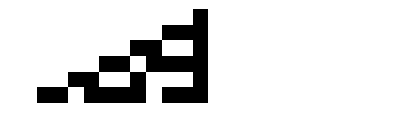

```mathematica
seq = {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0 }
partSeq = Partition[seq,3,1]
rules = {
{1,1,1}-> 0,
{1,1,0} -> 0,
{1,0,1} -> 0,
{1,0,0} -> 1,
{0,1,1} -> 1,
{0,1,0} -> 1,
{0,0,1} -> 1,
{0,0,0} -> 0
}
(*partSeq /.rules     (* that is the 2nd line *)*)
result = {seq}
For[i = 0,i<5,i++,
partSeq = Partition[Last[result],3,1, {1,-1}, 0];
Print[partSeq];
partSeq = partSeq/.rules;
result = Append[result, partSeq]
]
Print[result]
ArrayPlot[result]
```